```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
<<FeynCalc`
On[Assert];
```

FeynCalc 10.0.0 (development version). For help, use the online documentation, check out the wiki or visit the forum.

Please check our FAQ for answers to some common FeynCalc questions and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 2.0.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please evaluate FeynHelpersHowToCite[] to learn how to correctly cite this work.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*QGLoadInsertions[];
out=QGCreateAmp[2,{"phi[p1]", "phi[p2]", "phi[p3]","phi[q1]","phi[q2]","phi[q3]"}->{},QGLoopMomentum->k,QGOptions->{"onepi","notadpole"},QGModel->"3dFull446",QGShowOutput->False]

gotThemOut=QGConvertToFC[out[[1]],DiracChainJoin->True]
Length[gotThemOut]*)
```

1300

```mathematica
QGLoadInsertions[];
out=QGCreateAmp[2,{"phi[p]"}->{"phi[p]"},QGLoopMomentum->k,QGOptions->{"onepi","notadpole"},QGModel->"3dFull446",QGShowOutput->False]

gotThemOut=QGConvertToFC[out[[1]],DiracChainJoin->True]
```

{/home/f/fraser-taliente/dphil/largeNmodels/3dYukawa/amplitudes.m,/home/f/fraser-taliente/dphil/largeNmodels/3dYukawa/diagrams.m}

Warning! Some insertion rules are missing.

{1/8 QGPropagator(phi(1,k1),phi(2,-k1),m) QGPropagator(phi(3,k2),phi(4,-k2),m) QGPolarization(phi(-2,p),m) QGPolarization(phi(-1,p),m) QGVertex(phi(-1,p),phi(-2,-p),phi(1,k1),phi(2,-k1),phi(3,k2),phi(4,-k2)),1/4 QGVertex(phi(2,-k1),phi(4,k1),phi(5,k2),phi(6,-k2)) QGPropagator(phi(1,k1),phi(2,-k1),m) QGPropagator(phi(3,-k1),phi(4,k1),m) QGVertex(phi(-1,p),phi(-2,-p),phi(1,k1),phi(3,-k1)) QGPropagator(phi(5,k2),phi(6,-k2),m) QGPolarization(phi(-2,p),m) QGPolarization(phi(-1,p),m),-1/2 QGPropagator(phi(1,k1),phi(2,-k1),m) QGPropagator(phi(3,-k1),phi(4,k1),m) QGVertex(phi(-1,p),phi(-2,-p),phi(1,k1),phi(3,-k1)) QGPolarization(phi(-2,p),m) QGPolarization(phi(-1,p),m) QGPropagator(psi(5,k2),psibar(6,-k2),M) QGVertex(psibar(6,-k2),psi(5,k2),phi(2,-k1),phi(4,k1)),-1/2 QGPropagator(phi(5,k2),phi(6,-k2),m) QGPolarization(phi(-2,p),m) QGPolarization(phi(-1,p),m) QGPropagator(psi(1,k1),psibar(2,-k1),M) QGPropagator(psi(3,k1),psibar(4,-k1),M) QGVertex(psibar(2,-k1),psi(3,k1),phi(5,k2),phi(6,-k2)) QGVertex(psibar(4,-k1),psi(1,k1),phi(-1,p),phi(-2,-p)),1/6 QGPropagator(phi(3,-k1),phi(4,k1),m) QGPropagator(phi(5,-k2),phi(6,k2),m) QGPolarization(phi(-2,p),m) QGPolarization(phi(-1,p),m) QGVertex(phi(-2,-p),phi(2,-k1-k2+p),phi(4,k1),phi(6,k2)) QGVertex(phi(-1,p),phi(1,k1+k2-p),phi(3,-k1),phi(5,-k2)) QGPropagator(phi(1,k1+k2-p),phi(2,-k1-k2+p),m),-QGPolarization(phi(-2,p),m) QGPolarization(phi(-1,p),m) QGPropagator(psi(3,-k1),psibar(4,k1),M) QGPropagator(psi(5,k2),psibar(6,-k2),M) QGPropagator(phi(1,k1+k2-p),phi(2,-k1-k2+p),m) QGVertex(psibar(4,k1),psi(5,k2),phi(-2,-p),phi(2,-k1-k2+p)) QGVertex(psibar(6,-k2),psi(3,-k1),phi(-1,p),phi(1,k1+k2-p))}

```mathematica
QGPrepareDiagramsTeX[out[[2]],"dias.tex",Style->"TikZ-Feynman"]
(*or QGPrepareDiagramsTeX[out[[2]],"Dias",Split->True]*)``
```

dias.tex

```mathematica
insertions ={QGPropagator[q_[i_,p_],qbar_[j_,_],mass_]/;MemberQ[{{El,Ael},{Mu,Amu},{Tau,Atau}, {psi, psibar}},{q,qbar}]:>I DCHN[GSD[p]+mass,FCMakeIndex["QGIDir",i],FCMakeIndex["QGIDir",j]] FAD[{p,mass}],
QGPropagator[scalar_[i_,p_],scalar_[j_,_],mass_]/;MemberQ[{{phi,phi}},{scalar,scalar}]:>I FAD[{p,mass}],
QGVertex[scalar_[i_, p_],scalar_[j_, q_],scalar_[k_,r_],scalar_[l_, s_]]/;MemberQ[{{phi}},{scalar}]:> -I g, 
QGVertex[scalar_[i_, p_],scalar_[j_, q_],scalar_[k_,r_],scalar_[l_, s_],scalar_[t_,r_],scalar_[u_, s_]]/;MemberQ[{{phi}},{scalar}]:> -I h, 
QGVertex[quarkbar_[l_, s_],quark_[k_,r_],scalar_[i_, p_],scalar_[j_, q_]]/;MemberQ[{{phi, psi,psibar}},{scalar, quark, quarkbar}]:> -I λ DIDelta[FCMakeIndex["QGIDir",k],FCMakeIndex["QGIDir",l]], 
(*++++++++++++++++Incoming fermion (u spinor) polarization++++++++++++++++*)
QGPolarization[q_[i_,p_],mass_]/;MemberQ[{Q,Qi,Qj,El,Mu,Tau,psi},q]:> DCHN[FCMakeIndex["QGIDir",i],Spinor[Momentum[p,D],mass]]/;FreeQ[$QGCommonInsertionsExternalColors,q[p]]&&OddQ[i],
(*++++++++++++++++Outgoing fermion (ubar spinor) polarization++++++++++++++++*)
QGPolarization[q_[i_,p_],mass_]/;MemberQ[{Q,Qi,Qj,El,Mu,Tau,psi},q]:>DCHN[Spinor[Momentum[p,D],mass],FCMakeIndex["QGIDir",i]]/;FreeQ[$QGCommonInsertionsExternalColors,q[p]]&&EvenQ[i],
QGPolarization[scalar_[i_,p_],mass_]/;MemberQ[{{scalar}},{phi}]:> 1
}
```

{QGPropagator(q_(i_,p_),qbar_(j_,_),mass_)/;MemberQ[(El | Ael
Mu | Amu
Tau | Atau
psi | psibar),{q,qbar}]:>(ⅈ (mass+γ·p)_(FCMakeIndex(QGIDir,i)FCMakeIndex(QGIDir,j)))/(p^2-mass^2),QGPropagator(scalar_(i_,p_),scalar_(j_,_),mass_)/;MemberQ[(phi | phi),{scalar,scalar}]:>ⅈ/(p^2-mass^2),QGVertex(scalar_(i_,p_),scalar_(j_,q_),scalar_(k_,r_),scalar_(l_,s_))/;MemberQ[(phi),{scalar}]:>-ⅈ g,QGVertex(scalar_(i_,p_),scalar_(j_,q_),scalar_(k_,r_),scalar_(l_,s_),scalar_(t_,r_),scalar_(u_,s_))/;MemberQ[(phi),{scalar}]:>-ⅈ h,QGVertex(quarkbar_(l_,s_),quark_(k_,r_),scalar_(i_,p_),scalar_(j_,q_))/;MemberQ[(phi | psi | psibar),{scalar,quark,quarkbar}]:>-ⅈ λ δ_(FCMakeIndex(QGIDir,k)FCMakeIndex(QGIDir,l)),QGPolarization(q_(i_,p_),mass_)/;MemberQ[{Q,Qi,Qj,El,Mu,Tau,psi},q]:>(φ(p,mass))_(FCMakeIndex(QGIDir,i))/;FreeQ[$QGCommonInsertionsExternalColors,q(p)]∧OddQ[i],QGPolarization(q_(i_,p_),mass_)/;MemberQ[{Q,Qi,Qj,El,Mu,Tau,psi},q]:>(φ(p,mass))_(FCMakeIndex(QGIDir,i))/;FreeQ[$QGCommonInsertionsExternalColors,q(p)]∧EvenQ[i],QGPolarization(scalar_(i_,p_),mass_)/;MemberQ[(scalar),{phi}]:>1}

```mathematica
insertionsCT ={QGPropagator[q_[i_,p_],qbar_[j_,_],mass_]/;MemberQ[{{El,Ael},{Mu,Amu},{Tau,Atau}, {psi, psibar}},{q,qbar}]:>I DCHN[GSD[p]+mass,FCMakeIndex["QGIDir",i],FCMakeIndex["QGIDir",j]] FAD[{p,mass}] + ct( DCHN[(GSD[p]+mass).(I dZψ2 GSD[p]-I dZMψ2 M ).(GSD[p]+mass),FCMakeIndex["QGIDir",i],FCMakeIndex["QGIDir",j]] I^2 FAD[{p,mass}]^2),
QGPropagator[scalar_[i_,p_],scalar_[j_,_],mass_]/;MemberQ[{{phi,phi}},{scalar,scalar}]:>I FAD[{p,mass}] + ct(I(dZϕ2 Pair[Momentum[p,D],Momentum[p,D]] - (dZmϕ2)m^2)I^2 FAD[{p,mass}]^2),
QGVertex[scalar_[i_, p_],scalar_[j_, q_],scalar_[k_,r_],scalar_[l_, s_]]/;MemberQ[{{phi}},{scalar}]:> -I g  + ct (-I g)(dZgϕ4), 
QGVertex[scalar_[i_, p_],scalar_[j_, q_],scalar_[k_,r_],scalar_[l_, s_],scalar_[m_,t_],scalar_[n_, u_]]/;MemberQ[{{phi}},{scalar}]:> -I h  + ct (-I h)(dZhϕ6), 
QGVertex[quarkbar_[l_, s_],quark_[k_,r_],scalar_[i_, p_],scalar_[j_, q_]]/;MemberQ[{{phi, psi,psibar}},{scalar, quark, quarkbar}]:> -I λ DIDelta[FCMakeIndex["QGIDir",k],FCMakeIndex["QGIDir",l]]*(1+ct (dZλϕ2ψ2)), 
(*++++++++++++++++Incoming fermion (u spinor) polarization++++++++++++++++*)
QGPolarization[q_[i_,p_],mass_]/;MemberQ[{Q,Qi,Qj,El,Mu,Tau,psi},q]:> DCHN[FCMakeIndex["QGIDir",i],Spinor[Momentum[p,D],mass]]/;FreeQ[$QGCommonInsertionsExternalColors,q[p]]&&OddQ[i],
(*++++++++++++++++Outgoing fermion (ubar spinor) polarization++++++++++++++++*)
QGPolarization[q_[i_,p_],mass_]/;MemberQ[{Q,Qi,Qj,El,Mu,Tau,psi},q]:>DCHN[Spinor[Momentum[p,D],mass],FCMakeIndex["QGIDir",i]]/;FreeQ[$QGCommonInsertionsExternalColors,q[p]]&&EvenQ[i],
QGPolarization[scalar_[i_,p_],mass_]/;MemberQ[{{scalar}},{phi}]:> 1,

(*++++++++++++++++Incoming antifermion (vbar spinor) polarization++++++++++++++++*)
QGPolarization[qbar_[i_,p_],mass_]/;MemberQ[{Qbar,Qibar,Qjbar,Ael,Amu,Atau,psibar},qbar]:>DCHN[Spinor[-Momentum[p,D],mass],FCMakeIndex["QGIDir",i]]/;FreeQ[$QGCommonInsertionsExternalColors,qbar[p]]&&OddQ[i],
(*++++++++++++++++Outgoing antifermion (v spinor) polarization++++++++++++++++*)QGPolarization[qbar_[i_,p_],mass_]/;MemberQ[{Qbar,Qibar,Qjbar,Ael,Amu,Atau,psibar},qbar]:>DCHN[FCMakeIndex["QGIDir",i],Spinor[-Momentum[p,D],mass]]/;FreeQ[$QGCommonInsertionsExternalColors,qbar[p]]&&EvenQ[i]
}
```

{QGPropagator(q_(i_,p_),qbar_(j_,_),mass_)/;MemberQ[(El | Ael
Mu | Amu
Tau | Atau
psi | psibar),{q,qbar}]:>ct (ⅈ^2 (1/(p^2-mass^2))^2 ((mass+γ·p).(ⅈ dZψ2 γ·p-ⅈ dZMψ2 M).(mass+γ·p))_(FCMakeIndex(QGIDir,i)FCMakeIndex(QGIDir,j)))+(ⅈ (mass+γ·p)_(FCMakeIndex(QGIDir,i)FCMakeIndex(QGIDir,j)))/(p^2-mass^2),QGPropagator(scalar_(i_,p_),scalar_(j_,_),mass_)/;MemberQ[(phi | phi),{scalar,scalar}]:>ct (ⅈ ⅈ^2 (1/(p^2-mass^2))^2 (dZϕ2 p^2-dZmϕ2 m^2))+ⅈ/(p^2-mass^2),QGVertex(scalar_(i_,p_),scalar_(j_,q_),scalar_(k_,r_),scalar_(l_,s_))/;MemberQ[(phi),{scalar}]:>ct dZgϕ4 (-ⅈ g)-ⅈ g,QGVertex(scalar_(i_,p_),scalar_(j_,q_),scalar_(k_,r_),scalar_(l_,s_),scalar_(m_,t_),scalar_(n_,u_))/;MemberQ[(phi),{scalar}]:>ct dZhϕ6 (-ⅈ h)-ⅈ h,QGVertex(quarkbar_(l_,s_),quark_(k_,r_),scalar_(i_,p_),scalar_(j_,q_))/;MemberQ[(phi | psi | psibar),{scalar,quark,quarkbar}]:>-ⅈ λ (ct dZλϕ2ψ2+1) δ_(FCMakeIndex(QGIDir,k)FCMakeIndex(QGIDir,l)),QGPolarization(q_(i_,p_),mass_)/;MemberQ[{Q,Qi,Qj,El,Mu,Tau,psi},q]:>(φ(p,mass))_(FCMakeIndex(QGIDir,i))/;FreeQ[$QGCommonInsertionsExternalColors,q(p)]∧OddQ[i],QGPolarization(q_(i_,p_),mass_)/;MemberQ[{Q,Qi,Qj,El,Mu,Tau,psi},q]:>(φ(p,mass))_(FCMakeIndex(QGIDir,i))/;FreeQ[$QGCommonInsertionsExternalColors,q(p)]∧EvenQ[i],QGPolarization(scalar_(i_,p_),mass_)/;MemberQ[(scalar),{phi}]:>1,QGPolarization(qbar_(i_,p_),mass_)/;MemberQ[{Qbar,Qibar,Qjbar,Ael,Amu,Atau,psibar},qbar]:>(φ(-p,mass))_(FCMakeIndex(QGIDir,i))/;FreeQ[$QGCommonInsertionsExternalColors,qbar(p)]∧OddQ[i],QGPolarization(qbar_(i_,p_),mass_)/;MemberQ[{Qbar,Qibar,Qjbar,Ael,Amu,Atau,psibar},qbar]:>(φ(-p,mass))_(FCMakeIndex(QGIDir,i))/;FreeQ[$QGCommonInsertionsExternalColors,qbar(p)]∧EvenQ[i]}

```mathematica
phiStruct[i_,j_]:=phidelta[FCMakeIndex["c",{i,j},c]]
psiStruct[i_,j_]:=psidelta[FCMakeIndex["c",{i,j},c]]
gStruct[i_,j_,k_,l_]:=gO[FCMakeIndex["c",{i,j,k,l},c]]
λStruct[i_,j_,k_,l_]:=λO[FCMakeIndex["c",{i,j,k,l},c]]
hStruct[i_,j_,k_,l_,m_,n_]:=hO[FCMakeIndex["c",{i,j,k,l,m,n},c]]
```

```mathematica
insertionsWithSubs={QGPropagator[q_[i_,p_],qbar_[j_,_],mass_]/;MemberQ[{{El,Ael},{Mu,Amu},{Tau,Atau}, {psi, psibar}},{q,qbar}]:>((I DCHN[GSD[p]+mass,FCMakeIndex["QGIDir",i],FCMakeIndex["QGIDir",j]] FAD[{p,mass}] + ct( DCHN[(GSD[p]+mass).(I dZψ2 GSD[p]-I dZMψ2 M ).(GSD[p]+mass),FCMakeIndex["QGIDir",i],FCMakeIndex["QGIDir",j]] I^2 FAD[{p,mass}]^2))) psiStruct[i,j],

QGPropagator[scalar_[i_,p_],scalar_[j_,_],mass_]/;MemberQ[{{phi,phi}},{scalar,scalar}]:>(I FAD[{p,mass}] + ct(I(dZϕ2 Pair[Momentum[p,D],Momentum[p,D]] - (dZmϕ2)m^2)I^2 FAD[{p,mass}]^2))phiStruct[i,j],

QGVertex[scalar_[i_, p_],scalar_[j_, q_],scalar_[k_,r_],scalar_[l_, s_]]/;MemberQ[{{phi}},{scalar}]:> -I g gStruct[i,j,k,l] , 

QGVertex[scalar_[i_, p_],scalar_[j_, q_],scalar_[k_,r_],scalar_[l_, s_],scalar_[m_,t_],scalar_[n_, u_]]/;MemberQ[{{phi}},{scalar}]:> -I h hStruct[i,j,k,l,m,n], 
QGVertex[quarkbar_[l_, s_],quark_[k_,r_],scalar_[i_, p_],scalar_[j_, q_]]/;MemberQ[{{phi, psi,psibar}},{scalar, quark, quarkbar}]:> -I λ( DIDelta[FCMakeIndex["QGIDir",k],FCMakeIndex["QGIDir",l]]) λStruct[l,k,i,j], 

(*++++++++++++++++Incoming fermion (u spinor) polarization++++++++++++++++*)
QGPolarization[q_[i_,p_],mass_]/;MemberQ[{Q,Qi,Qj,El,Mu,Tau,psi},q]:> DCHN[FCMakeIndex["QGIDir",i],Spinor[Momentum[p,D],mass]]/;FreeQ[$QGCommonInsertionsExternalColors,q[p]]&&OddQ[i],
(*++++++++++++++++Outgoing fermion (ubar spinor) polarization++++++++++++++++*)
QGPolarization[q_[i_,p_],mass_]/;MemberQ[{Q,Qi,Qj,El,Mu,Tau,psi},q]:>DCHN[Spinor[Momentum[p,D],mass],FCMakeIndex["QGIDir",i]]/;FreeQ[$QGCommonInsertionsExternalColors,q[p]]&&EvenQ[i],
QGPolarization[scalar_[i_,p_],mass_]/;MemberQ[{{scalar}},{phi}]:> 1,
(*++++++++++++++++Incoming antifermion (vbar spinor) polarization++++++++++++++++*)
QGPolarization[qbar_[i_,p_],mass_]/;MemberQ[{Qbar,Qibar,Qjbar,Ael,Amu,Atau,psibar},qbar]:>DCHN[Spinor[-Momentum[p,D],mass],FCMakeIndex["QGIDir",i]]/;FreeQ[$QGCommonInsertionsExternalColors,qbar[p]]&&OddQ[i],
(*++++++++++++++++Outgoing antifermion (v spinor) polarization++++++++++++++++*)QGPolarization[qbar_[i_,p_],mass_]/;MemberQ[{Qbar,Qibar,Qjbar,Ael,Amu,Atau,psibar},qbar]:>DCHN[FCMakeIndex["QGIDir",i],Spinor[-Momentum[p,D],mass]]/;FreeQ[$QGCommonInsertionsExternalColors,qbar[p]]&&EvenQ[i]
}



insertionsForGraph ={QGPropagator[q_[i_,p_],qbar_[j_,_],mass_]/;MemberQ[{{El,Ael},{Mu,Amu},{Tau,Atau}, {psi, psibar}},{q,qbar}]:>psiStruct[i,j],

QGPropagator[scalar_[i_,p_],scalar_[j_,_],mass_]/;MemberQ[{{phi,phi}},{scalar,scalar}]:>phiStruct[i,j],

QGVertex[scalar_[i_, p_],scalar_[j_, q_],scalar_[k_,r_],scalar_[l_, s_]]/;MemberQ[{{phi}},{scalar}]:> gStruct[i,j,k,l] , 

QGVertex[scalar_[i_, p_],scalar_[j_, q_],scalar_[k_,r_],scalar_[l_, s_],scalar_[m_,t_],scalar_[n_, u_]]/;MemberQ[{{phi}},{scalar}]:> hStruct[i,j,k,l,m,n], 
QGVertex[quarkbar_[l_, s_],quark_[k_,r_],scalar_[i_, p_],scalar_[j_, q_]]/;MemberQ[{{phi, psi,psibar}},{scalar, quark, quarkbar}]:>  λStruct[l,k,i,j], 


(*++++++++++++++++Incoming fermion (u spinor) polarization++++++++++++++++*)
QGPolarization[q_[i_,p_],mass_]/;MemberQ[{Q,Qi,Qj,El,Mu,Tau,psi},q]:>ext[psiin[FCMakeIndex["c",i,c]]]/;FreeQ[$QGCommonInsertionsExternalColors,q[p]]&&OddQ[i],
(*++++++++++++++++Outgoing fermion (ubar spinor) polarization++++++++++++++++*)
QGPolarization[q_[i_,p_],mass_]/;MemberQ[{Q,Qi,Qj,El,Mu,Tau,psi},q]:>ext[psiout[FCMakeIndex["c",i,c]]]/;FreeQ[$QGCommonInsertionsExternalColors,q[p]]&&EvenQ[i],
(*++++++++++++++++Incoming antifermion (vbar spinor) polarization++++++++++++++++*)
QGPolarization[qbar_[i_,p_],mass_]/;MemberQ[{Qbar,Qibar,Qjbar,Ael,Amu,Atau,psibar},qbar]:>ext[psibarin[FCMakeIndex["c",i,c]]]/;FreeQ[$QGCommonInsertionsExternalColors,qbar[p]]&&OddQ[i],
(*++++++++++++++++Outgoing antifermion (v spinor) polarization++++++++++++++++*)QGPolarization[qbar_[i_,p_],mass_]/;MemberQ[{Qbar,Qibar,Qjbar,Ael,Amu,Atau,psibar},qbar]:>ext[psibarout[FCMakeIndex["c",i,c]]]/;FreeQ[$QGCommonInsertionsExternalColors,qbar[p]]&&EvenQ[i],

QGPolarization[scalar_[i_,p_],mass_]/;MemberQ[{phi},scalar]:> ext[phiin[FCMakeIndex["c",i,c]]]/;OddQ[i],
QGPolarization[scalar_[i_,p_],mass_]/;MemberQ[{phi},scalar]:> ext[phiout[FCMakeIndex["c",i,c]]]/;EvenQ[i]
};
```

{QGPropagator(q_(i_,p_),qbar_(j_,_),mass_)/;MemberQ[(El | Ael
Mu | Amu
Tau | Atau
psi | psibar),{q,qbar}]:>psiStruct(i,j) (ct (ⅈ^2 (1/(p^2-mass^2))^2 ((mass+γ·p).(ⅈ dZψ2 γ·p-ⅈ dZMψ2 M).(mass+γ·p))_(FCMakeIndex(QGIDir,i)FCMakeIndex(QGIDir,j)))+(ⅈ (mass+γ·p)_(FCMakeIndex(QGIDir,i)FCMakeIndex(QGIDir,j)))/(p^2-mass^2)),QGPropagator(scalar_(i_,p_),scalar_(j_,_),mass_)/;MemberQ[(phi | phi),{scalar,scalar}]:>phiStruct(i,j) (ct (ⅈ ⅈ^2 (1/(p^2-mass^2))^2 (dZϕ2 p^2-dZmϕ2 m^2))+ⅈ/(p^2-mass^2)),QGVertex(scalar_(i_,p_),scalar_(j_,q_),scalar_(k_,r_),scalar_(l_,s_))/;MemberQ[(phi),{scalar}]:>-ⅈ g gStruct(i,j,k,l),QGVertex(scalar_(i_,p_),scalar_(j_,q_),scalar_(k_,r_),scalar_(l_,s_),scalar_(m_,t_),scalar_(n_,u_))/;MemberQ[(phi),{scalar}]:>-ⅈ h hStruct(i,j,k,l,m,n),QGVertex(quarkbar_(l_,s_),quark_(k_,r_),scalar_(i_,p_),scalar_(j_,q_))/;MemberQ[(phi | psi | psibar),{scalar,quark,quarkbar}]:>-ⅈ λ δ_(FCMakeIndex(QGIDir,k)FCMakeIndex(QGIDir,l)) λStruct(l,k,i,j),QGPolarization(q_(i_,p_),mass_)/;MemberQ[{Q,Qi,Qj,El,Mu,Tau,psi},q]:>(φ(p,mass))_(FCMakeIndex(QGIDir,i))/;FreeQ[$QGCommonInsertionsExternalColors,q(p)]∧OddQ[i],QGPolarization(q_(i_,p_),mass_)/;MemberQ[{Q,Qi,Qj,El,Mu,Tau,psi},q]:>(φ(p,mass))_(FCMakeIndex(QGIDir,i))/;FreeQ[$QGCommonInsertionsExternalColors,q(p)]∧EvenQ[i],QGPolarization(scalar_(i_,p_),mass_)/;MemberQ[(scalar),{phi}]:>1,QGPolarization(qbar_(i_,p_),mass_)/;MemberQ[{Qbar,Qibar,Qjbar,Ael,Amu,Atau,psibar},qbar]:>(φ(-p,mass))_(FCMakeIndex(QGIDir,i))/;FreeQ[$QGCommonInsertionsExternalColors,qbar(p)]∧OddQ[i],QGPolarization(qbar_(i_,p_),mass_)/;MemberQ[{Qbar,Qibar,Qjbar,Ael,Amu,Atau,psibar},qbar]:>(φ(-p,mass))_(FCMakeIndex(QGIDir,i))/;FreeQ[$QGCommonInsertionsExternalColors,qbar(p)]∧EvenQ[i]}

```mathematica
killAllToJustSF = #[[1]] ->1 &/@insertionsCT;
Assert[(#[[1]] &/@insertions)===(#[[1]] &/@insertionsCT)]
```

Assert::asrtf: Assertion (#1⟦1⟧&)/@insertions===(#1⟦1⟧&)/@insertionsCT failed.

```mathematica
(*reps={dZla->dZλ + 2 dZϕ + 2dZψ, dZgam->dZg + 4dZϕ}*)
```

```mathematica
gotThemOut[[1]]/.insertionsForGraph//InputForm
```

(ext[phiin[c[cMinus1]]]*ext[phiout[c[cMinus2]]]*hO[{c[cMinus1], c[cMinus2], c[c1], c[c2], c[c3], c[c4]}]*phidelta[{c[c1], c[c2]}]*phidelta[{c[c3], c[c4]}])/8

```mathematica
justGraphStructure=List@@Simplify[((#/.insertionsForGraph)/(#/.killAllToJustSF)) ]&/@gotThemOut
```

{{ext(phiin(c(cMinus1))),ext(phiout(c(cMinus2))),hO({c(cMinus1),c(cMinus2),c(c1),c(c2),c(c3),c(c4)}),phidelta({c(c1),c(c2)}),phidelta({c(c3),c(c4)})},{ext(phiin(c(cMinus1))),ext(phiout(c(cMinus2))),gO({c(c2),c(c4),c(c5),c(c6)}),gO({c(cMinus1),c(cMinus2),c(c1),c(c3)}),phidelta({c(c1),c(c2)}),phidelta({c(c3),c(c4)}),phidelta({c(c5),c(c6)})},{ext(phiin(c(cMinus1))),ext(phiout(c(cMinus2))),gO({c(cMinus1),c(cMinus2),c(c1),c(c3)}),phidelta({c(c1),c(c2)}),phidelta({c(c3),c(c4)}),psidelta({c(c5),c(c6)}),λO({c(c6),c(c5),c(c2),c(c4)})},{ext(phiin(c(cMinus1))),ext(phiout(c(cMinus2))),phidelta({c(c5),c(c6)}),psidelta({c(c1),c(c2)}),psidelta({c(c3),c(c4)}),λO({c(c2),c(c3),c(c5),c(c6)}),λO({c(c4),c(c1),c(cMinus1),c(cMinus2)})},{ext(phiin(c(cMinus1))),ext(phiout(c(cMinus2))),gO({c(cMinus1),c(c1),c(c3),c(c5)}),gO({c(cMinus2),c(c2),c(c4),c(c6)}),phidelta({c(c1),c(c2)}),phidelta({c(c3),c(c4)}),phidelta({c(c5),c(c6)})},{ext(phiin(c(cMinus1))),ext(phiout(c(cMinus2))),phidelta({c(c1),c(c2)}),psidelta({c(c3),c(c4)}),psidelta({c(c5),c(c6)}),λO({c(c4),c(c5),c(cMinus2),c(c2)}),λO({c(c6),c(c3),c(cMinus1),c(c1)})}}

```mathematica
justGraphStructure[[1]]//InputForm
```

{ext[phiin[c[cMinus1]]], ext[phiout[c[cMinus2]]], hO[{c[cMinus1], c[cMinus2], c[c1], c[c2], c[c3], c[c4]}], phidelta[{c[c1], c[c2]}], phidelta[{c[c3], c[c4]}]}

```mathematica
vertexMap={hO[a__]->Nothing,gO[b__]->Nothing,λO[c__]->Nothing}
```

{hO(a__)→Nothing,gO(b__)→Nothing,λO(c__)→Nothing}

```mathematica
First/@vertices
```

vertices

```mathematica
Select[graph, !edges[#, externals[[1]]]&]
```

Select::normal: Nonatomic expression expected at position 1 in Select[graph,¬edges(#1,externals⟦1⟧)&].

Select[graph,¬edges(#1,externals⟦1⟧)&]

```mathematica
makeGraph[graph_]:=Module[{(*externals,edges,vertices,deltaMaps,extMaps, fixed*)},
externals =Cases[graph, ext[__]];
edges = Cases[graph,phidelta[__]|psidelta[__]];
vertices = Cases[graph,hO[__]|gO[__]|λO[__]];
deltaMaps =Join@@(Thread[Rest[#[[1]]]->First[#[[1]]]] &/@vertices);

extMaps ={ext[phiin[a_]]:>DirectedEdge[ext[phiin[a ]],a/.deltaMaps, ϕ],
ext[phiout[a_]]:>DirectedEdge[a/.deltaMaps,ext[phiout[a]], ϕ],
ext[psiin[a_]]:>DirectedEdge[ext[psiin[a]],a/.deltaMaps,ψ],
ext[psiout[a_]]:>DirectedEdge[a/.deltaMaps,ext[psiout[a]], ψ],
ext[psibarin[a_]]:>DirectedEdge[a/.deltaMaps,ext[psibarin[a]], ψ],
ext[psibarout[a_]]:>DirectedEdge[ext[psibarout[a]],a/.deltaMaps,ψ]
};
propMaps = {
phidelta[{a_,b_}]->DirectedEdge[a,b,ϕ],
psidelta[{a_,b_}]->DirectedEdge[a,b,ψ]
};
fixed=Join[edges/.deltaMaps,(externals/.extMaps)];
graphNoAnnotations=Graph[fixed/.propMaps,EdgeStyle->{DirectedEdge[a_,b_,ϕ]->{Black,Dashed},DirectedEdge[a_,b_,ψ]->{Black}}];

Graph[graphNoAnnotations,VertexLabels->Join[(#->First[#]&/@externals ),#[[1,1]]->Head[#]&/@vertices],VertexCoordinates->{externals[[1]]->{0,0},externals[[2]]->{1,0}}]
];
```

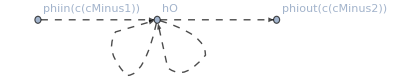

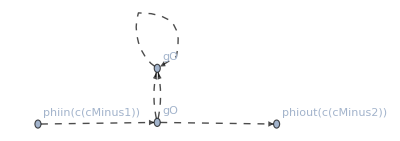

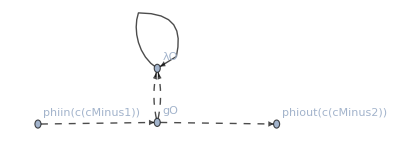

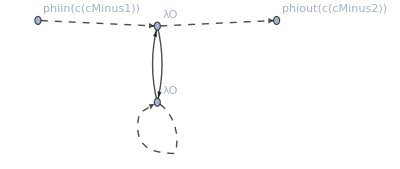

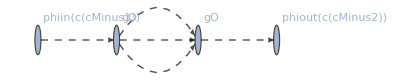

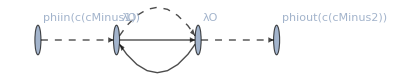

{Null,Null,Null,Null,Null,Null}

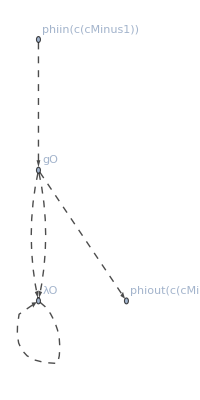

```mathematica
Print@*makeGraph/@justGraphStructure
```

```mathematica
Graph[{{UndirectedEdge[c1,c1,ϕ],UndirectedEdge[c1,c1,ϕ]}}]
```

Graph[(c1c1ϕ | c1c1ϕ)]

```mathematica
Graph[{aa<->aa,aa<->aa}]//InputForm
```

Graph[{aa}, {UndirectedEdge[aa, aa], UndirectedEdge[aa, aa]}]

```mathematica
gotThemOut/.insertionsWithSubs//DiracChainJoin//FullSimplify
```

{(ⅈ h hO({c(cMinus1),c(cMinus2),c(c1),c(c2),c(c3),c(c4)}) ((ct (dZmϕ2 m^2-dZϕ2 k1^2))/(k1^2-m^2)+1) ((ct (dZmϕ2 m^2-dZϕ2 k2^2))/(k2^2-m^2)+1) phidelta({c(c1),c(c2)}) phidelta({c(c3),c(c4)}))/(8 (k1^2-m^2) (k2^2-m^2)),1/(4 (k1^2-m^2)^2 (k2^2-m^2))ⅈ g^2 gO({c(c2),c(c4),c(c5),c(c6)}) gO({c(cMinus1),c(cMinus2),c(c1),c(c3)}) ((ct (dZmϕ2 m^2-dZϕ2 k1^2))/(k1^2-m^2)+1) ((ct (dZmϕ2 m^2-dZϕ2 k1^2))/(k1^2-m^2)+1) ((ct (dZmϕ2 m^2-dZϕ2 k2^2))/(k2^2-m^2)+1) phidelta({c(c1),c(c2)}) phidelta({c(c3),c(c4)}) phidelta({c(c5),c(c6)}),1/(2 (k1^2-m^2)^2 (k2^2-M^2))g λ ((ct tr((M+γ·k2).(ⅈ dZψ2 γ·k2-ⅈ dZMψ2 M).(M+γ·k2)))/(k2^2-M^2)-ⅈ tr(M+γ·k2)) gO({c(cMinus1),c(cMinus2),c(c1),c(c3)}) ((ct (dZmϕ2 m^2-dZϕ2 k1^2))/(k1^2-m^2)+1) ((ct (dZmϕ2 m^2-dZϕ2 k1^2))/(k1^2-m^2)+1) phidelta({c(c1),c(c2)}) phidelta({c(c3),c(c4)}) psidelta({c(c5),c(c6)}) λO({c(c6),c(c5),c(c2),c(c4)}),1/(2 (k2^2-m^2))λ^2 (1/(k1^2-M^2))^2 ((ct (2 tr((M+γ·k1).(M+γ·k1).(ⅈ dZψ2 γ·k1-ⅈ dZMψ2 M).(M+γ·k1))+(ⅈ ct tr((M+γ·k1).(ⅈ dZψ2 γ·k1-ⅈ dZMψ2 M).(M+γ·k1).(M+γ·k1).(ⅈ dZψ2 γ·k1-ⅈ dZMψ2 M).(M+γ·k1)))/(k1^2-M^2)))/(k1^2-M^2)-ⅈ tr((M+γ·k1).(M+γ·k1))) ((ct (dZmϕ2 m^2-dZϕ2 k2^2))/(k2^2-m^2)+1) phidelta({c(c5),c(c6)}) psidelta({c(c1),c(c2)}) psidelta({c(c3),c(c4)}) λO({c(c2),c(c3),c(c5),c(c6)}) λO({c(c4),c(c1),c(cMinus1),c(cMinus2)}),1/(6 (k1^2-m^2) (k2^2-m^2) ((k1+k2-p)^2-m^2))ⅈ g^2 gO({c(cMinus1),c(c1),c(c3),c(c5)}) gO({c(cMinus2),c(c2),c(c4),c(c6)}) ((ct (dZmϕ2 m^2-dZϕ2 k1^2))/(k1^2-m^2)+1) ((ct (dZmϕ2 m^2-dZϕ2 k2^2))/(k2^2-m^2)+1) ((ct (dZmϕ2 m^2-dZϕ2 (k1+k2-p)^2))/((k1+k2-p)^2-m^2)+1) phidelta({c(c1),c(c2)}) phidelta({c(c3),c(c4)}) phidelta({c(c5),c(c6)}),1/((k1^2-M^2) (k2^2-M^2) ((k1+k2-p)^2-m^2))λ^2 (-ⅈ tr((M-γ·k1).(M+γ·k2))+(ct tr((M+γ·k2).(M-γ·k1).(-ⅈ (dZMψ2 M+dZψ2 γ·k1)).(M-γ·k1)))/(k1^2-M^2)+(ct (tr((M-γ·k1).(M+γ·k2).(ⅈ dZψ2 γ·k2-ⅈ dZMψ2 M).(M+γ·k2))+(ⅈ ct tr((M-γ·k1).(-ⅈ (dZMψ2 M+dZψ2 γ·k1)).(M-γ·k1).(M+γ·k2).(-ⅈ (dZMψ2 M-dZψ2 γ·k2)).(M+γ·k2)))/(k1^2-M^2)))/(k2^2-M^2)) ((ct (dZmϕ2 m^2-dZϕ2 (k1+k2-p)^2))/((k1+k2-p)^2-m^2)+1) phidelta({c(c1),c(c2)}) psidelta({c(c3),c(c4)}) psidelta({c(c5),c(c6)}) λO({c(c4),c(c5),c(cMinus2),c(c2)}) λO({c(c6),c(c3),c(cMinus1),c(c1)})}

```mathematica
stdQGCreateAmp[nLoops_,input_]:=QGCreateAmp[nLoops,input,QGLoopMomentum->k,QGModel->"3dFull446",QGOptions->{"onepi","notadpole"},QGShowOutput->False];
makePhiPhi[nLoops_]:=Module[{done,results},
 done=stdQGCreateAmp[nLoops,{"phi[p]"}->{"phi[p]"}];
results = {ϕϕ,nLoops}->runFinal[{ϕϕ,nLoops},done];
PutAppend[results,"/tmp/output.out"];
results
];
makePsiPsi[nLoops_]:=Module[{done,results}, 
 done=stdQGCreateAmp[nLoops,{"psi[p]"}->{"psi[p]"}];
results = {ψψb,nLoops}->runFinal[{ψψb,nLoops},done];
PutAppend[results,"/tmp/output.out"];
results
];

makeLam[nLoops_]:=Module[{done,results},
 done=stdQGCreateAmp[nLoops,{"phi[p1]", "psi[p2]"}->{"phi[q1]","psi[q2]"}];
results = {λ,nLoops}->runFinal[{λ,nLoops},done];
PutAppend[results,"/tmp/output.out"];
results
];
makeg[nLoops_]:=Module[{done,results},
 done=stdQGCreateAmp[nLoops,{"phi[p1]", "phi[p2]"}->{"phi[q1]","phi[q2]"}];
results = {g,nLoops}->runFinal[{g,nLoops},done];
PutAppend[results,"/tmp/output.out"];
results
];
makeh[nLoops_]:=Module[{done,results},
 done=stdQGCreateAmp[nLoops,{"phi[p1]", "phi[p2]", "phi[p3]"}->{"phi[q1]","phi[q2]","phi[q3]"}];
results = {h,nLoops}->runFinal[{h,nLoops},done];
PutAppend[results,"/tmp/output.out"];
results
];
```

```mathematica
traceRules={DiracTrace[1] -> Tr1s, DiracTrace[DiracGamma[Momentum[k1_, D], D]] -> 0,  DiracTrace[DiracGamma[Momentum[mom1_, D], D] . DiracGamma[Momentum[mom2_, D], D]] -> Tr1s*Pair[Momentum[mom1, D], Momentum[mom2, D]],(*DiracTrace[DiracGamma[Momentum[mom1_, D], D] . DiracGamma[Momentum[mom2_, D], D] . DiracGamma[Momentum[mom3_, D], D]] -> 2*Tr3[Momentum[mom1, D], Momentum[mom2, D], Momentum[mom3, D]],*)DiracTrace[DiracGamma[Momentum[mom1_, D], D] . DiracGamma[Momentum[mom2_, D], D] . DiracGamma[Momentum[mom3_, D], D] . DiracGamma[Momentum[mom4_, D], D]] -> 2*DiracTrace[DiracGamma[Momentum[mom1, D], D] . DiracGamma[Momentum[mom2, D], D] . DiracGamma[Momentum[mom3, D], D] . DiracGamma[Momentum[mom4, D], D], DiracTraceEvaluate->True, TraceOfOne->Tr1s],
DiracTrace[DiracGamma[LorentzIndex[arb_,D],D]]->0 (*This can come from kslash Tr[kslash^3] -> gamm_mu Tr[gamm^mu] k^2*)}
renormalisationPoints=<|ϕϕ->{},ψψb->{},λ->{p1->0,p2->0,q1->0,q2->0},g->{p1->0,p2->0,q1->0,q2->0},h->{p1->0,p2->0,p3->0,q1->0,q2->0,q3->0}|>
runFinal[{head_Symbol,nLoops_Integer},listOfAmps_List]:=Module[{andConv,fetchFCish,fullInsertions, removeIndexStructure, justGraphStructure,keepToOrder,andConvAllCt,symFacs,simplified,traces,renoPoint,diracedUp,prepped, internalMomenta,fcMLTID,appliedDiracSimplifyAgain, tracesSecondTime, withSymmetryFactors,uniqs, justUniqueDiags,uniqueDiagsLoopExtracted,justBadBits,justFinalBitsContainingLIs,justLoops, justLoopsDuped,equalDiagsGrouped,representativeDiagrams,mapDWSFToRepresentative,mapAllToSomething,testRun},

renoPoint=renormalisationPoints[head];
fetchFCish =QGConvertToFC[listOfAmps[[1]],DiracChainJoin->True];
symFacs = fetchFCish/.killAllToJustSF; 
Print[ {head,nLoops} ->renoPoint, ". There are ", Length[symFacs], " diagrams."];

keepToOrder=(*key is nLoops*)<|2->0, 1->1,0->5|>;
fullInsertions =fetchFCish/.insertionsWithSubs;
removeIndexStructure =fullInsertions /.(#[__]->1 &/@ {phidelta, psidelta, gO, λO,hO});

If[nLoops >2,
andConv=removeIndexStructure/.ct->0;
,
Print["    ","Keeping to order ", keepToOrder];
andConv =Normal[Simplify[Series[#, {ct,0,keepToOrder[nLoops]}]],Series]& /@ removeIndexStructure;
];



diracedUp=andConv//DiracChainJoin;

justGraphStructure=List@@Simplify[((#/.insertionsForGraph)/(#/.killAllToJustSF)) ]&/@fetchFCish;



Print["    ","Running firstDiracSimplify:"];
simplified=DiracSimplify[diracedUp(* breaks ordering. DOT[Spinor[__], b___, Spinor[__]]->b *)/.Spinor[a__]->1/.renoPoint (*/.DiracTrace[inside_]->DiracTrace[inside, TraceOfOne->gammaMatrixDim]*), DiracTrace->True (*Simplify inside DiracTrace*),DiracTraceEvaluate->False (*But do not evaluate it*),SirlinSimplify->False,InsideDiracTrace->False]//FCTraceExpand;
traces = Union[Cases[simplified, DiracTrace[__],Infinity]];

Print["    ","Applying traceRules to the ", Length[traces], " traces"];
prepped = simplified/.traceRules;
internalMomenta=Sort@DeleteCases[Union@Cases[prepped, Momentum[mom_, D]->mom, Infinity], Except[k1|k2|k3|k3|k4|k5|k6|k7|k8|k9|k10]];
Print["    ","Internal momenta detected are: ",internalMomenta];
fcMLTID = FCMultiLoopTID[#, internalMomenta, FDS->False,ApartFF->False, DiracSimplify->False, Dimension->D]&/@prepped;

Print["    ","Applying DiracSimplify again after tensor integral decomposition"];
appliedDiracSimplifyAgain = FDS@(FCTraceFactor[DiracSimplify[#, DiracTrace->True (*Simplify inside DiracTrace*) ,DiracTraceEvaluate->False(*But do not evaluate it*),SirlinSimplify->False,InsideDiracTrace->False (*not working inside DiracTrace*)]] /.traceRules) &/@ fcMLTID;
(*GroupBy[(*all the same*)]*)
tracesSecondTime= Union[Cases[appliedDiracSimplifyAgain, DiracTrace[__],Infinity]];
Print["    ","Remaining traces: ",Short[ tracesSecondTime,5]];
withSymmetryFactors =Association[Simplify@MapThread[diagWithSF[head,nLoops, #2]->#1&, {appliedDiracSimplifyAgain, Range@Length[appliedDiracSimplifyAgain]}]];

uniqs =GroupBy[withSymmetryFactors, Identity]; (*GroupBy[assoc,f] gives an association whose keys are the distinct f[elemi] and whose values are subassociations of the association assoc.*)
Print["    ","Reduction in diagram count due to overlap between diagrams: ",
				 Length[withSymmetryFactors] ->Length[uniqs]];

equalDiagsGrouped = Values[Keys/@uniqs];
representativeDiagrams = First/@equalDiagsGrouped;
mapDWSFToRepresentative= Join@@Map[Thread[# -> First[#]] &, equalDiagsGrouped];

justUniqueDiags=Keys[uniqs];
Assert[justUniqueDiags === (withSymmetryFactors/@representativeDiagrams)];

uniqueDiagsLoopExtracted=AssociationMap[FCLoopExtract[#, internalMomenta, loopIntegral, PaVe->False, MultiLoop->False,FCLoopSplit->{2,3},FCLoopBasisSplit->True, FCI->True,FCLoopIBPReducableQ->False]&,justUniqueDiags];
(*"MultiLoop is an option for FCLoopIsolate. When set to True, FCLoopIsolate will
isolate only such loop integrals, that depend on all of the given loop
momenta. Integrals that depend only on some of the loop momenta will be
treated as non-loop terms and remain non-isolated.";*)

justBadBits=First/@uniqueDiagsLoopExtracted;
justFinalBitsContainingLIs=#[[2]]&/@uniqueDiagsLoopExtracted;
Print["    ","Are there no bad bits: ", Union[Values[justBadBits]] ==={0}];

justLoopsDuped =Join@@Values[#[[3]] &/@uniqueDiagsLoopExtracted];
justLoops =Union[justLoopsDuped];
Print["    ","Reduction in loopIntegrals count due to overlap between loopIntegrals: ", Length[justLoopsDuped] ->Length[justLoops]];

mapAllToSomething=((#*0) +something)& /@ justFinalBitsContainingLIs;
testRun= #/.mapAllToSomething &/@ withSymmetryFactors;
Assert[Union[Values[testRun]]=={something}];
(*Test that these really do replace all the right things*)

fetchContractionStructure[thisStructure_]:=Module[{thisAmp,theseDeltas},
thisAmp=thisStructure/.ext[__]->Nothing;
theseDeltas =Cases[thisAmp,phidelta[__]|psidelta[__],Infinity];
thisAmp/.Thread[theseDeltas->Nothing]/.(#[[1,1]]->#[[1,2]]&/@theseDeltas)
];


Return@<|"loopIntsToDo"->justLoops,"diagsToEvaluateNoSFs"->justFinalBitsContainingLIs,"diagsNoSFs"->withSymmetryFactors,"loopsExtractedNoSFs"->uniqueDiagsLoopExtracted,"simpWithSF"->simplified, "traces"->{traces, tracesSecondTime}, "initialInserted"->diracedUp,"fromQG"->fetchFCish,"symFacs"->symFacs, "mapDWSFToRepresentative"->mapDWSFToRepresentative,"justStructure"->justGraphStructure,"contractionStructure"->(fetchContractionStructure/@justGraphStructure)|>
];
```

{tr(1)→Tr1s,tr(γ·k1_)→0,tr((γ·mom1_).(γ·mom2_))→Tr1s (mom1·mom2),tr((γ·mom1_).(γ·mom2_).(γ·mom3_).(γ·mom4_))→2 Tr1s ((mom1·mom4) (mom2·mom3)-(mom1·mom3) (mom2·mom4)+(mom1·mom2) (mom3·mom4)),tr(γ^arb_)→0}

<|ϕϕ→{},ψψb→{},λ→{p1→0,p2→0,q1→0,q2→0},g→{p1→0,p2→0,q1→0,q2→0},h→{p1→0,p2→0,p3→0,q1→0,q2→0,q3→0}|>

```mathematica
GroupBy[gam2[{h,2}]["diagsToEvaluateNoSFs"],Identity, Length]//Length
```

<|1/4 ⅈ h^2 loopIntegral(1/((k1^2-m^2)^2),{k1}) loopIntegral(1/(k2^2-m^2),{k2})→1,1/6 ⅈ h^2 loopIntegral(1/(((k1+k2)^2-m^2).(k1^2-m^2).(k2^2-m^2)),{k1,k2})→1,1/4 ⅈ g^2 h loopIntegral(1/((k1^2-m^2)^2),{k1}) loopIntegral(1/((k2^2-m^2)^2),{k2})→1,-1/2 ⅈ h λ^2 M^2 Tr1s loopIntegral(1/((k1^2-M^2)^2),{k1}) loopIntegral(1/((k2^2-m^2)^2),{k2})-1/2 ⅈ h λ^2 Tr1s loopIntegral(k1^2/((k1^2-M^2)^2),{k1}) loopIntegral(1/((k2^2-m^2)^2),{k2})→1,1/2 ⅈ g^2 h loopIntegral(1/((k1^2-m^2)^3),{k1}) loopIntegral(1/(k2^2-m^2),{k2})→1,-ⅈ g h λ M Tr1s loopIntegral(1/((k1^2-m^2)^3),{k1}) loopIntegral(1/(k2^2-M^2),{k2})→1,1/2 ⅈ g^2 h loopIntegral(1/((k1^2-m^2).((k1+k2)^2-m^2).(k2^2-m^2)^2),{k1,k2})→1,-ⅈ h λ^2 M^2 Tr1s loopIntegral(1/((k1^2-M^2).((k1+k2)^2-M^2).(k2^2-m^2)^2),{k1,k2})-ⅈ h λ^2 Tr1s loopIntegral(k1^2/((k1^2-M^2).((k1+k2)^2-M^2).(k2^2-m^2)^2),{k1,k2})-ⅈ h λ^2 Tr1s loopIntegral((k1·k2)/((k1^2-M^2).((k1+k2)^2-M^2).(k2^2-m^2)^2),{k1,k2})→1,1/2 ⅈ g^2 h loopIntegral(1/((k1^2-m^2)^2.((k1-k2)^2-m^2).(k2^2-m^2)),{k1,k2})→1,1/2 ⅈ g^4 loopIntegral(1/((k1^2-m^2)^3),{k1}) loopIntegral(1/((k2^2-m^2)^2),{k2})→1,-ⅈ g^2 λ^2 M^2 Tr1s loopIntegral(1/((k1^2-m^2)^3),{k1}) loopIntegral(1/((k2^2-M^2)^2),{k2})-ⅈ g^2 λ^2 Tr1s loopIntegral(1/((k1^2-m^2)^3),{k1}) loopIntegral(k2^2/((k2^2-M^2)^2),{k2})→1,-3/2 ⅈ g λ^3 M Tr1s loopIntegral(k1^2/((k1^2-M^2)^3),{k1}) loopIntegral(1/((k2^2-m^2)^2),{k2})-1/2 ⅈ g λ^3 M^3 Tr1s loopIntegral(1/((k1^2-M^2)^3),{k1}) loopIntegral(1/((k2^2-m^2)^2),{k2})→1,1/2 ⅈ g^4 loopIntegral(1/((k1^2-m^2)^4),{k1}) loopIntegral(1/(k2^2-m^2),{k2})→1,-ⅈ g^3 λ M Tr1s loopIntegral(1/((k1^2-m^2)^4),{k1}) loopIntegral(1/(k2^2-M^2),{k2})→1,-3 ⅈ λ^4 M^2 Tr1s loopIntegral(k1^2/((k1^2-M^2)^4),{k1}) loopIntegral(1/(k2^2-m^2),{k2})-1/2 ⅈ λ^4 Tr1s loopIntegral(k1^4/((k1^2-M^2)^4),{k1}) loopIntegral(1/(k2^2-m^2),{k2})-1/2 ⅈ λ^4 M^4 Tr1s loopIntegral(1/((k1^2-M^2)^4),{k1}) loopIntegral(1/(k2^2-m^2),{k2})→1,ⅈ g^4 loopIntegral(1/((k2^2-m^2)^2.((k1+k2)^2-m^2).(k1^2-m^2)^2),{k1,k2})→1,-3 ⅈ g λ^3 M Tr1s loopIntegral(k2^2/((k2^2-M^2)^2.((k1+k2)^2-M^2).(k1^2-m^2)^2),{k1,k2})-2 ⅈ g λ^3 M Tr1s loopIntegral((k1·k2)/((k2^2-M^2)^2.((k1+k2)^2-M^2).(k1^2-m^2)^2),{k1,k2})-ⅈ g λ^3 M^3 Tr1s loopIntegral(1/((k2^2-M^2)^2.((k1+k2)^2-M^2).(k1^2-m^2)^2),{k1,k2})→1,-3 ⅈ g λ^3 M Tr1s loopIntegral(k1^2/((k2^2-m^2)^2.((k1+k2)^2-M^2).(k1^2-M^2)^2),{k1,k2})-2 ⅈ g λ^3 M Tr1s loopIntegral((k1·k2)/((k2^2-m^2)^2.((k1+k2)^2-M^2).(k1^2-M^2)^2),{k1,k2})-ⅈ g λ^3 M^3 Tr1s loopIntegral(1/((k2^2-m^2)^2.((k1+k2)^2-M^2).(k1^2-M^2)^2),{k1,k2})→1,-ⅈ λ^4 M^2 Tr1s loopIntegral(k1^2/((k2^2-M^2)^2.((k1+k2)^2-m^2).(k1^2-M^2)^2),{k1,k2})-ⅈ λ^4 M^2 Tr1s loopIntegral(k2^2/((k2^2-M^2)^2.((k1+k2)^2-m^2).(k1^2-M^2)^2),{k1,k2})-ⅈ λ^4 Tr1s loopIntegral((k1^2 k2^2)/((k2^2-M^2)^2.((k1+k2)^2-m^2).(k1^2-M^2)^2),{k1,k2})+4 ⅈ λ^4 M^2 Tr1s loopIntegral((k1·k2)/((k2^2-M^2)^2.((k1+k2)^2-m^2).(k1^2-M^2)^2),{k1,k2})-ⅈ λ^4 M^4 Tr1s loopIntegral(1/((k2^2-M^2)^2.((k1+k2)^2-m^2).(k1^2-M^2)^2),{k1,k2})→1,1/2 ⅈ g^4 loopIntegral(1/((k2^2-m^2).((k1+k2)^2-m^2).(k1^2-m^2)^3),{k1,k2})→1,-ⅈ g^2 λ^2 M^2 Tr1s loopIntegral(1/((k2^2-M^2).((k1+k2)^2-M^2).(k1^2-m^2)^3),{k1,k2})-ⅈ g^2 λ^2 Tr1s loopIntegral(k2^2/((k2^2-M^2).((k1+k2)^2-M^2).(k1^2-m^2)^3),{k1,k2})-ⅈ g^2 λ^2 Tr1s loopIntegral((k1·k2)/((k2^2-M^2).((k1+k2)^2-M^2).(k1^2-m^2)^3),{k1,k2})→1,-3 ⅈ λ^4 M^2 Tr1s loopIntegral(k1^2/((k2^2-M^2).((k1+k2)^2-m^2).(k1^2-M^2)^3),{k1,k2})+3 ⅈ λ^4 M^2 Tr1s loopIntegral((k1·k2)/((k2^2-M^2).((k1+k2)^2-m^2).(k1^2-M^2)^3),{k1,k2})+ⅈ λ^4 Tr1s loopIntegral((k1^2 (k1·k2))/((k2^2-M^2).((k1+k2)^2-m^2).(k1^2-M^2)^3),{k1,k2})-ⅈ λ^4 M^4 Tr1s loopIntegral(1/((k2^2-M^2).((k1+k2)^2-m^2).(k1^2-M^2)^3),{k1,k2})→1|>

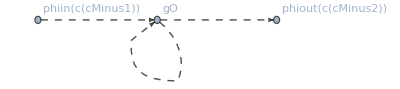

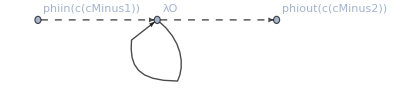

{Null,Null}

```mathematica
Print@*makeGraph/@phiphi2[{ϕϕ,2}]["justStructure"]
```

```mathematica
answers =phiphi2[{ϕϕ,2}]["contractionStructure"]
```

{{hO({c(cMinus1),c(cMinus2),c(c2),c(c2),c(c4),c(c4)})},{gO({c(c2),c(c4),c(c6),c(c6)}),gO({c(cMinus1),c(cMinus2),c(c2),c(c4)})},{gO({c(cMinus1),c(cMinus2),c(c2),c(c4)}),λO({c(c6),c(c6),c(c2),c(c4)})},{λO({c(c2),c(c4),c(c6),c(c6)}),λO({c(c4),c(c2),c(cMinus1),c(cMinus2)})},{gO({c(cMinus1),c(c2),c(c4),c(c6)}),gO({c(cMinus2),c(c2),c(c4),c(c6)})},{λO({c(c4),c(c6),c(cMinus2),c(c2)}),λO({c(c6),c(c4),c(cMinus1),c(c2)})}}

{phidelta({c(c5),c(c6)}),psidelta({c(c1),c(c2)}),psidelta({c(c3),c(c4)}),λO({c(c2),c(c3),c(c5),c(c6)}),λO({c(c4),c(c1),c(cMinus1),c(cMinus2)})}

{phidelta({c(c5),c(c6)}),psidelta({c(c1),c(c2)}),psidelta({c(c3),c(c4)})}

{λO({c(c2),c(c4),c(c6),c(c6)}),λO({c(c4),c(c2),c(cMinus1),c(cMinus2)})}

```mathematica
analyseStructure[test_]
```

```mathematica
/.phidelta[{a,b}]
```

{{hO({c(cMinus1),c(cMinus2),c(c1),c(c2),c(c3),c(c4)}),phidelta({c(c1),c(c2)}),phidelta({c(c3),c(c4)})},{gO({c(c2),c(c4),c(c5),c(c6)}),gO({c(cMinus1),c(cMinus2),c(c1),c(c3)}),phidelta({c(c1),c(c2)}),phidelta({c(c3),c(c4)}),phidelta({c(c5),c(c6)})},{gO({c(cMinus1),c(cMinus2),c(c1),c(c3)}),phidelta({c(c1),c(c2)}),phidelta({c(c3),c(c4)}),psidelta({c(c5),c(c6)}),λO({c(c6),c(c5),c(c2),c(c4)})},{phidelta({c(c5),c(c6)}),psidelta({c(c1),c(c2)}),psidelta({c(c3),c(c4)}),λO({c(c2),c(c3),c(c5),c(c6)}),λO({c(c4),c(c1),c(cMinus1),c(cMinus2)})},{gO({c(cMinus1),c(c1),c(c3),c(c5)}),gO({c(cMinus2),c(c2),c(c4),c(c6)}),phidelta({c(c1),c(c2)}),phidelta({c(c3),c(c4)}),phidelta({c(c5),c(c6)})},{phidelta({c(c1),c(c2)}),psidelta({c(c3),c(c4)}),psidelta({c(c5),c(c6)}),λO({c(c4),c(c5),c(cMinus2),c(c2)}),λO({c(c6),c(c3),c(cMinus1),c(c1)})}}

```mathematica
phiphi2 = Association[makePhiPhi/@Range[2] ]//EchoTiming;
psipsi2= Association[makePsiPsi/@Range[2]]//EchoTiming;
```

Warning! Some insertion rules are missing.

{ϕϕ,1}→{}. There are 2 diagrams.

Keeping to order <|2→0,1→1,0→5|>

Running firstDiracSimplify:

Applying traceRules to the 2 traces

Internal momenta detected are: {k1}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 2→2

Are there no bad bits: True

Reduction in loopIntegrals count due to overlap between loopIntegrals: 6→6

Warning! Some insertion rules are missing.

{ϕϕ,2}→{}. There are 6 diagrams.

Keeping to order <|2→0,1→1,0→5|>

Running firstDiracSimplify:

Applying traceRules to the 4 traces

Internal momenta detected are: {k1,k2}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 6→6

Are there no bad bits: True

Reduction in loopIntegrals count due to overlap between loopIntegrals: 12→9

0.458776

Warning! Some insertion rules are missing.

{ψψb,1}→{}. There are 1 diagrams.

Keeping to order <|2→0,1→1,0→5|>

Running firstDiracSimplify:

Applying traceRules to the 0 traces

Internal momenta detected are: {k1}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 1→1

Are there no bad bits: True

Reduction in loopIntegrals count due to overlap between loopIntegrals: 3→3

Warning! Some insertion rules are missing.

{ψψb,2}→{}. There are 3 diagrams.

Keeping to order <|2→0,1→1,0→5|>

Running firstDiracSimplify:

Applying traceRules to the 2 traces

Internal momenta detected are: {k1,k2}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 3→3

Are there no bad bits: True

Reduction in loopIntegrals count due to overlap between loopIntegrals: 6→5

0.354692

```mathematica
phiphi2
```

{{ϕϕ,1}→runFinal({ϕϕ,1},{/home/f/fraser-taliente/amplitudes.m,/home/f/fraser-taliente/diagrams.m}),{ϕϕ,2}→runFinal({ϕϕ,2},{/home/f/fraser-taliente/amplitudes.m,/home/f/fraser-taliente/diagrams.m})}

```mathematica
lam2 =Association[ makeLam/@Range[2] ]//EchoTiming;
gam2 =Association[ makeg/@Range[2]] //EchoTiming;
```

Warning! Some insertion rules are missing.

{λ,1}→{p1→0,p2→0,q1→0,q2→0}. There are 3 diagrams.

Keeping to order <|2→0,1→1,0→5|>

Running firstDiracSimplify:

Applying traceRules to the 0 traces

Internal momenta detected are: {k1}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 3→2

Are there no bad bits: True

Reduction in loopIntegrals count due to overlap between loopIntegrals: 8→8

Warning! Some insertion rules are missing.

{λ,2}→{p1→0,p2→0,q1→0,q2→0}. There are 25 diagrams.

Keeping to order <|2→0,1→1,0→5|>

Running firstDiracSimplify:

Applying traceRules to the 4 traces

Internal momenta detected are: {k1,k2}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 25→15

Are there no bad bits: True

Reduction in loopIntegrals count due to overlap between loopIntegrals: 31→23

1.55284

Warning! Some insertion rules are missing.

{g,1}→{p1→0,p2→0,q1→0,q2→0}. There are 7 diagrams.

Keeping to order <|2→0,1→1,0→5|>

Running firstDiracSimplify:

Applying traceRules to the 2 traces

Internal momenta detected are: {k1}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 7→3

Are there no bad bits: True

Reduction in loopIntegrals count due to overlap between loopIntegrals: 11→10

Warning! Some insertion rules are missing.

{g,2}→{p1→0,p2→0,q1→0,q2→0}. There are 57 diagrams.

Keeping to order <|2→0,1→1,0→5|>

Running firstDiracSimplify:

Applying traceRules to the 5 traces

Internal momenta detected are: {k1,k2}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 57→13

Are there no bad bits: True

Reduction in loopIntegrals count due to overlap between loopIntegrals: 29→21

1.87674

```mathematica
gam2 =Association[ makeh/@Range[2] ]//EchoTiming;
```

Warning! Some insertion rules are missing.

{h,1}→{p1→0,p2→0,p3→0,q1→0,q2→0,q3→0}. There are 60 diagrams.

Keeping to order <|2→0,1→1,0→5|>

Running firstDiracSimplify:

Applying traceRules to the 2 traces

Internal momenta detected are: {k1}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 60→3

Are there no bad bits: True

Reduction in loopIntegrals count due to overlap between loopIntegrals: 11→10

Warning! Some insertion rules are missing.

{h,2}→{p1→0,p2→0,p3→0,q1→0,q2→0,q3→0}. There are 1300 diagrams.

Keeping to order <|2→0,1→1,0→5|>

Running firstDiracSimplify:

Applying traceRules to the 5 traces

Internal momenta detected are: {k1,k2}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 1300→22

Are there no bad bits: True

Reduction in loopIntegrals count due to overlap between loopIntegrals: 53→41

40.594

```mathematica
studyThis=gam2[{h,2}];
```

```mathematica
contractionStructures =Association@MapIndexed[#2[[1]](*diagramNumber*)->#1 &,Transpose[{studyThis["justStructure"],studyThis["contractionStructure"]}]];
```

```mathematica
externals=Union@Cases[contractionStructures[[1]], ext[__],Infinity]
killExternals =#[[1,1]]->e&/@externals
```

{ext(phiin(c(cMinus1))),ext(phiin(c(cMinus3))),ext(phiin(c(cMinus5))),ext(phiout(c(cMinus2))),ext(phiout(c(cMinus4))),ext(phiout(c(cMinus6)))}

{c(cMinus1)→e,c(cMinus3)→e,c(cMinus5)→e,c(cMinus2)→e,c(cMinus4)→e,c(cMinus6)→e}

```mathematica
getTensorContractionButForgetExternal[currentVersion_List]:=Module[{thisOne, tP, indices, contractedOnes, contractionRules},
tP=( TensorProduct@@currentVersion)/.{λO[__]->λo, gO[__]->go,hO[__]->ho};
indices=Flatten[First/@currentVersion];
contractedOnes =Union@Cases[indices,c[_]];
contractionRules =First/@Position[indices, #,{1}]&/@contractedOnes;
TensorContract[tP,contractionRules]//TensorReduce
];
```

```mathematica
killExternals
```

{c(cMinus1)→e,c(cMinus3)→e,c(cMinus5)→e,c(cMinus2)→e,c(cMinus4)→e,c(cMinus6)→e}

```mathematica
Sort[#[[2]]/.killExternals]&/@contractionStructures[[1]]
```

{ext(phiin(e)),hO({e,e,c(c2),c(c4),c(c6),c(c6)})}

```mathematica
indirectMethodMid=GroupBy[Sort[#[[2]]/.killExternals]&/@(contractionStructures),Identity];
doneIndirectMethod=getTensorContractionButForgetExternal/@Keys[indirectMethodMid];
```

```mathematica
Print[Length[contractionStructures]->Length[indirectMethodMid]->Length[Length/@GroupBy[doneIndirectMethod, Identity]]]
```

1300→30→27

```mathematica
groupDirect=GroupBy[contractionStructures,getTensorContractionButForgetExternal@Sort[#[[2]]/.killExternals]&]//EchoTiming;
Length[groupDirect]
```

1.1525

27

```mathematica
(*Length/@groupDirect*)
```

```mathematica
$Assumptions={λo∈Arrays[{n,n,n,n}, Reals,{Symmetric[{1,2}],Symmetric[{3,4}]}],go∈Arrays[{n,n,n,n}, Reals,Symmetric[{1,2,3,4}]],ho∈Arrays[{n,n,n,n,n,n}, Reals,Symmetric[{1,2,3,4,5,6}]]}
(*$Assumptions={λo∈Arrays[{n,n,n,n}, Reals],go∈Arrays[{n,n,n,n}, Reals],ho∈Arrays[{n,n,n,n,n,n}, Reals]}*)
```

{λo∈Arrays[{n,n,n,n},ℝ,(Cycles[(1 | 2)] | 1
Cycles[(3 | 4)] | 1)],go∈Arrays[{n,n,n,n},ℝ,Symmetric[{1,2,3,4}]],ho∈Arrays[{n,n,n,n,n,n},ℝ,Symmetric[{1,2,3,4,5,6}]]}

```mathematica
currentGroup=groupDirect[[-20]];
currentGroup[[1;;3]]
```

<|87→{{ext(phiin(c(cMinus1))),ext(phiin(c(cMinus3))),ext(phiin(c(cMinus5))),ext(phiout(c(cMinus2))),ext(phiout(c(cMinus4))),ext(phiout(c(cMinus6))),hO({c(cMinus5),c(cMinus2),c(cMinus4),c(cMinus6),c(c6),c(c8)}),phidelta({c(c5),c(c6)}),phidelta({c(c7),c(c8)}),psidelta({c(c1),c(c2)}),psidelta({c(c3),c(c4)}),λO({c(c2),c(c3),c(cMinus3),c(c7)}),λO({c(c4),c(c1),c(cMinus1),c(c5)})},{hO({c(cMinus5),c(cMinus2),c(cMinus4),c(cMinus6),c(c6),c(c8)}),λO({c(c2),c(c4),c(cMinus3),c(c8)}),λO({c(c4),c(c2),c(cMinus1),c(c6)})}},89→{{ext(phiin(c(cMinus1))),ext(phiin(c(cMinus3))),ext(phiin(c(cMinus5))),ext(phiout(c(cMinus2))),ext(phiout(c(cMinus4))),ext(phiout(c(cMinus6))),hO({c(cMinus3),c(cMinus2),c(cMinus4),c(cMinus6),c(c6),c(c8)}),phidelta({c(c5),c(c6)}),phidelta({c(c7),c(c8)}),psidelta({c(c1),c(c2)}),psidelta({c(c3),c(c4)}),λO({c(c2),c(c3),c(cMinus5),c(c7)}),λO({c(c4),c(c1),c(cMinus1),c(c5)})},{hO({c(cMinus3),c(cMinus2),c(cMinus4),c(cMinus6),c(c6),c(c8)}),λO({c(c2),c(c4),c(cMinus5),c(c8)}),λO({c(c4),c(c2),c(cMinus1),c(c6)})}},91→{{ext(phiin(c(cMinus1))),ext(phiin(c(cMinus3))),ext(phiin(c(cMinus5))),ext(phiout(c(cMinus2))),ext(phiout(c(cMinus4))),ext(phiout(c(cMinus6))),hO({c(cMinus3),c(cMinus5),c(cMinus4),c(cMinus6),c(c6),c(c8)}),phidelta({c(c5),c(c6)}),phidelta({c(c7),c(c8)}),psidelta({c(c1),c(c2)}),psidelta({c(c3),c(c4)}),λO({c(c2),c(c3),c(cMinus2),c(c7)}),λO({c(c4),c(c1),c(cMinus1),c(c5)})},{hO({c(cMinus3),c(cMinus5),c(cMinus4),c(cMinus6),c(c6),c(c8)}),λO({c(c2),c(c4),c(cMinus2),c(c8)}),λO({c(c4),c(c2),c(cMinus1),c(c6)})}}|>

```mathematica
here=Keys[currentGroup](*Flatten[Position[contractionStructures,#]&/@currentGroup]*);
Print[here->Length[here], " and so ", Union[studyThis["simpWithSF"][[here]]], Union[studyThis["symFacs"][[here]]]];
```

{87,89,91,93,95,97,99,101,103,105,107,109,111,113,115}→15 and so {-(ⅈ h λ^2 (tr(1) M^2+2 tr(γ·k1) M+tr(γ·k2) M+tr((γ·k1).(γ·k2))+tr(1) k1^2))/((k1^2-M^2) (k2^2-m^2)^2 ((k1+k2)^2-M^2))}{-1}

```mathematica
getTensorStructureForThisStruct[thisOne_List]:=Module[{tP, indices,contractedOnes,contractionRules,contracted,freeOnesInGivenOrder,assignNumbers,correspondingPermutation},
tP=( TensorProduct@@thisOne)/.{λO[__]->λo, gO[__]->go,hO[__]->ho};
indices=Flatten[First/@thisOne];
contractedOnes =Union@Cases[indices/.killExternals,c[_]];
contractionRules =First/@Position[indices, #,{1}]&/@contractedOnes;
contracted =TensorContract[tP,contractionRules](*//TensorReduce*);

freeOnesInGivenOrder =DeleteCases[indices,Alternatives@@contractedOnes];
correspondingPermutation=FindPermutation[freeOnesInGivenOrder,Sort[freeOnesInGivenOrder]];
(*FindPermutation[expr1,expr2] gives a permutation that converts expr1 to expr2 for two expressions that differ only in the order of their arguments. We presently have an expression which is out of order; we must order them to become the new ones.*)

TensorTranspose[contracted,correspondingPermutation]//TensorReduce
];Print["May not work for λ!***************************************************"];
```

May not work for λ!***************************************************

```mathematica
currentGroup[[1]]
```

{{ext(phiin(c(cMinus1))),ext(phiin(c(cMinus3))),ext(phiin(c(cMinus5))),ext(phiout(c(cMinus2))),ext(phiout(c(cMinus4))),ext(phiout(c(cMinus6))),hO({c(cMinus5),c(cMinus2),c(cMinus4),c(cMinus6),c(c6),c(c8)}),phidelta({c(c5),c(c6)}),phidelta({c(c7),c(c8)}),psidelta({c(c1),c(c2)}),psidelta({c(c3),c(c4)}),λO({c(c2),c(c3),c(cMinus3),c(c7)}),λO({c(c4),c(c1),c(cMinus1),c(c5)})},{hO({c(cMinus5),c(cMinus2),c(cMinus4),c(cMinus6),c(c6),c(c8)}),λO({c(c2),c(c4),c(cMinus3),c(c8)}),λO({c(c4),c(c2),c(cMinus1),c(c6)})}}

```mathematica
eachTensored=getTensorStructureForThisStruct[#[[2]]]&/@currentGroup;
```

```mathematica
this = Total[eachTensored]//TensorReduce//FullSimplify;
```

```mathematica
(*this//TensorSymmetry does not work, so instead we just randomly test symmetries:*)
(TensorReduce[this-TensorTranspose[this,#]]===0 )&/@RandomChoice[Permutations[{1,2,3,4,5,6}],10]
```

{True,True,True,True,True,True,True,True,True,True}

```mathematica
(*Gamma matrices from the SUSY tensor model paper
aaas={{{0,-1},{1,0}}, {{0,1},{1,0}},{{1,0}, {0,-1}}}
aaas[[#]].aaas[[#]]&/@{1,2,3}*)
```

```mathematica
this-6! Symmetrize[eachTensored[[1]], Symmetric[{1,2,3,4,5,6}]]//TensorReduce//ByteCount
```

TensorTranspose::symmperm: Invalid permutation or symmetry generator {Cycles[{}],24}.

TensorTranspose::symmperm: Invalid permutation or symmetry generator {Cycles[(9 | 10 | 13)],24}.

TensorTranspose::symmperm: Invalid permutation or symmetry generator {Cycles[(4 | 5 | 6 | 9)],24}.

General::stop: Further output of TensorTranspose::symmperm will be suppressed during this calculation.

PermutationMax::permlist: Invalid permutation list {Cycles[{}],24}.

PermutationMax::permlist: Invalid permutation list {Cycles[(9 | 10 | 13)],24}.

PermutationMax::permlist: Invalid permutation list {Cycles[(4 | 5 | 6 | 9)],24}.

General::stop: Further output of PermutationMax::permlist will be suppressed during this calculation.

27432